Last modified on: Monday, July 9, 2018 at 11:05

Author Info

Nguyen Ton

Tuseeta Banejee

University of Virginia

Poster Session Content

Identify rotation of an image

The goal of project is identify how much an image is rotated compare to horizontal line

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Type in Text for Summary of Results
Type in more text
Type in more text

Type in Text
Type in Text
Type in Text

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Section Header

Type text here

Section Header

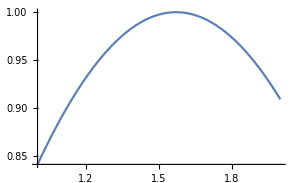
Plot[Sin[x],{x,1,2}]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

Provide one of:


The MNIST dataset is a good choice for training a new model, if you want to quickly prototype a new idea because the size of the images is small and their content is relatively simple. No need a very complex network with many layers that take a long time to train. If the model work well with simple handwritten digits, we can apply to real life images.
- MNIST data from ResourceData. With 60k images for training, 10k for testing and 10k for validation. Rotate 0, 90, 180, 270 deg. No cropping image here, because image size is 28x28, greyscale, so even after rotation, dimension still the same.
list=Keys[ResourceData["MNIST","TrainingData"]];
imgs=Table[list⟦i⟧,{i,1,Length[list]}];
rotateAll[x_]:=Table[ImageRotate[x, i Degree, Background→None],{i,0,270,90}];
rotatedImage=rotateAll/@imgs;
(* No need to crop 224x224. Because we rotate every 90 deg, it'll not change the image size *)
labelList=Table[ ToString[i],Length[imgs],{i,0,270,90}];
imageWithLabel=Thread[Flatten[rotatedImage] → Flatten[labelList]];
SetDirectory["/Users/nguyen/Documents"];
Export["mnist_trained_set.mx",imageWithLabel];
(* Test Set *)
test=Keys[ResourceData["MNIST","TestData"]];
rotatedTestSet=rotateAll/@test;
labelTestList=Table[ ToString[i],Length[test],{i,0,270,90}];
imageTestWithLabel=Thread[Flatten[rotatedTestSet] → Flatten[labelTestList]];
Export["mnist_test_set.mx",imageTestWithLabel];

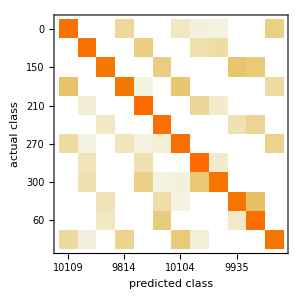
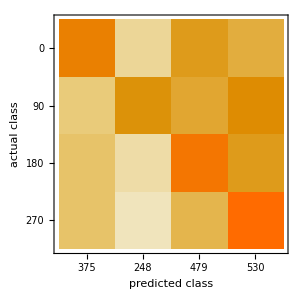
Result for MNIST with 90 deg rotation.
MNIST data with more rotations, from 0 to 330 degree in step of 30 deg.
Test on test data give accuracy of 97.7367
And the confusion matrix is shown below
-Graphics-


- Choose 4000 images for training set, 400 for testing and 400 for validation. With rotation of 0, 90, 180, 270 deg.
incept = NetTrain[inceptionNet, trainSet,All,BatchSize→ 100,Method→ “ADAM”,ValidationSet→validateSet,MaxTrainingRounds→80,TargetDevice→”GPU”]

- Result: accuracy 39.277%. 
Total training time 1.7 h. 
Rounds: 80
Batches: 12800
Method: ADAM
Confusion matrix plot:
-Graphics-

```mathematica
-
```

```mathematica
Choose 10k image for training from ImageNet, but result does not improve much.
- Download artifact 1000 images
```

google dataset
http://www.cs.ucf.edu/~aroshan/index_files/Dataset_PitOrlManh/zipped%20images/
choose part1,2
Now train 10k, test 1k and validate 1k

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information